#### This is based upon 16.09.22 Preparing 4 qubit cluster state v6 This is using the two peak trick to catch both E=-2,2

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];M=3;
Np=1;
dim=(Np+1)^M;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
Ham12=1.0*(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]);
Ham23=1.0*(KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]);
Ham123=1.0*(-KroneckerProduct[Sx,Id,Id]-KroneckerProduct[Id,Sx,Id]-KroneckerProduct[Id,Id,Sx]-(Np-2)*KroneckerProduct[Id,Id,Id]);
Cfunc[nc_,nd_,x_]=Which[(nc==0)&&(nd==0),Exp[-α^2/2],nd==0,(α^(nc))*Exp[-α^2/2]*(Cos[x]^nc)/Sqrt[(nc!)],nc==0,(α^(nd))*Exp[-α^2/2]*(Sin[x]^nd)/Sqrt[(nd!)],nc*nd≠0,(α^(nc+nd))*Exp[-α^2/2]*(Cos[x]^nc)*(Sin[x]^nd)/Sqrt[(nc!)*(nd!)]];
Eestfunc[nc_,nd_]=If[(nc==0)&&(nd==0),(Pi/2)/(2*τ),ArcCos[(nc-nd)/(nc+nd)]/(2*τ)];
```

```mathematica
α=1.0;τ=Pi/8;
sol=Eigensystem[Ham12];
En=sol[[1]];
Enstates=sol[[2]];
En12=sol[[1]];
Etgt12=0;
δtgt12=0.5;
MCfunc12[nc_,nd_]=Sum[Cfunc[nc,nd,En[[n]]*τ]*TensorProduct[Conjugate[Enstates[[n]]],Enstates[[n]]],{n,1,dim}];
α=1.0;τ=Pi/8;
sol=Eigensystem[Ham23];
En=sol[[1]];
Enstates=sol[[2]];
En23=sol[[1]];
Etgt23=0;
δtgt23=0.5;
MCfunc23[nc_,nd_]=Sum[Cfunc[nc,nd,En[[n]]*τ]*TensorProduct[Conjugate[Enstates[[n]]],Enstates[[n]]],{n,1,dim}];
α=1.0;τ=Pi/8;
sol=Eigensystem[Ham123];
En=sol[[1]];
Enstates=sol[[2]];
En123=sol[[1]];
Etgt123=2;
δtgt123=0.5;
MCfunc123[nc_,nd_]=Sum[Cfunc[nc,nd,En[[n]]*τ]*TensorProduct[Conjugate[Enstates[[n]]],Enstates[[n]]],{n,1,dim}];
```

```mathematica
En123
```

{6.,-6.,4.,4.,4.,-4.,-4.,-4.,2.,2.,-2.,2.,2.,2.,2.,-2.,-2.,-2.,-2.,-2.,8.88178×10^-15,4.07703×10^-15,1.34833×10^-15,8.88178×10^-16,4.44089×10^-16,4.44089×10^-16,0.}

```mathematica
ncdmax=5;
Ufix123[nc_,nd_]:=MatrixExp[I*(Mod[nc+nd,2])*Ham123*τ];
Aflip12=KroneckerProduct[MatrixExp[I*Sx*Pi/4],Id,Id];
Aflip34=KroneckerProduct[Id,Id,MatrixExp[I*Sx*Pi/4]];
Aflip123=KroneckerProduct[MatrixExp[I*Sz*Pi/2],Id,Id];
Chop[Sum[ConjugateTranspose[MCfunc12[nc,nd]].MCfunc12[nc,nd],{nc,0,ncdmax},{nd,0,ncdmax}]]
Chop[Sum[ConjugateTranspose[MCfunc23[nc,nd]].MCfunc23[nc,nd],{nc,0,ncdmax},{nd,0,ncdmax}]]
Chop[Sum[ConjugateTranspose[MCfunc123[nc,nd]].MCfunc123[nc,nd],{nc,0,ncdmax},{nd,0,ncdmax}]]
```

{{0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406}}

{{0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999406}}

{{0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928},{0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0},{0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0},{0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0},{0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0},{0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0},{0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.999972,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0.999689,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0,0},{0,0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0,0},{0,0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0,0},{0,0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0,0},{0,0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0,0},{0,0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689,0},{0.000282928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.999689}}

```mathematica
psi0=Normalize[Table[1-2*RandomReal[]+I*(1-2*RandomReal[]),{k,1,dim}]];
psi=psi0;
psic4=Normalize[ArrayReshape[Table[KroneckerDelta[k1,k2,k3]*Sqrt[Binomial[Np,k1]],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^M}][[1]]];
targetproj12=ArrayReshape[Table[KroneckerDelta[k1,k2]*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
targetproj23=ArrayReshape[Table[KroneckerDelta[k2,k3]*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
targetproj123z=ArrayReshape[Table[(KroneckerDelta[-2*k1-2*k2-2*k3+2*Np+2,2]+KroneckerDelta[-2*k1-2*k2-2*k3+2*Np+2,-2])*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
Urotzx=MatrixExp[-I*Sy*Pi/4];
Urotzxall=KroneckerProduct[Urotzx,Urotzx,Urotzx];
targetproj123=ConjugateTranspose[Urotzxall].targetproj123z.Urotzxall;
```

```mathematica
targetproj123z//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

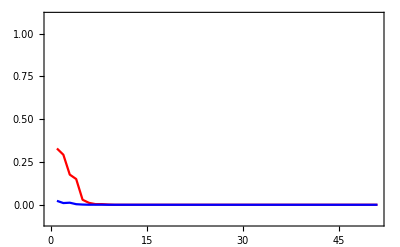

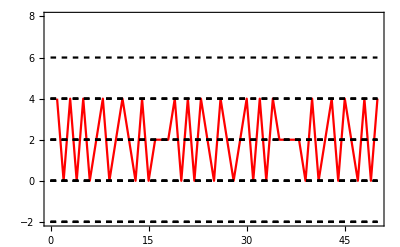

psi={0.0228888-0.0627635 ⅈ,-0.221269-0.143865 ⅈ,-0.11983-0.164191 ⅈ,0.0492489-0.0844767 ⅈ,1.26528×10^-9+2.69871×10^-10 ⅈ,-0.0492489+0.0844767 ⅈ,0.11983+0.164191 ⅈ,0.221269+0.143865 ⅈ,-0.0228888+0.0627635 ⅈ,0.17202+0.228341 ⅈ,0.0969414+0.226955 ⅈ,0.270518+0.0593878 ⅈ,-0.142719-0.101428 ⅈ,-8.31093×10^-10-2.16718×10^-10 ⅈ,0.142719+0.101428 ⅈ,-0.270518-0.0593878 ⅈ,-0.0969414-0.226955 ⅈ,-0.17202-0.228341 ⅈ,0.0228888-0.0627635 ⅈ,-0.221269-0.143865 ⅈ,-0.11983-0.164191 ⅈ,0.0492489-0.0844767 ⅈ,1.26528×10^-9+2.6987×10^-10 ⅈ,-0.0492489+0.0844767 ⅈ,0.11983+0.164191 ⅈ,0.221269+0.143865 ⅈ,-0.0228888+0.0627635 ⅈ}

```mathematica
(*X1X2X3 terms*)
nmax=50;
maxiter=1000;
mbuffer=0;
fidval=Conjugate[psi].targetproj123.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};
mc=0;
md=0;

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
nc=RandomInteger[{0,ncdmax}];
nd=RandomInteger[{0,ncdmax}];
ptry=RandomReal[];
psi1=MCfunc123[nc,nd].psi;
prob1=Norm[psi1]^2;
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];

psi=Ufix123[nc,nd].psi;

mc=mc+nc;
md=md+nd;

Eest=Eestfunc[mc,md];

If [(Abs[Eest-Etgt123]>=δtgt123)&&(mc+md>=mbuffer),
psi=Aflip123.psi;
mc=0;
md=0;

];

Eestlist=Append[Eestlist,Eest];

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj123.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
p1b=ListPlot[Eestlist,PlotStyle->{Red},PlotRange->{-2,8},Joined->True];
p3=Plot[DeleteDuplicates[En123],{x,0,nmax},PlotStyle->{Black,Dashing[0.01]}];
Show[p1]
Show[p1b,p3]
Print["psi=",Chop[psi]];
```

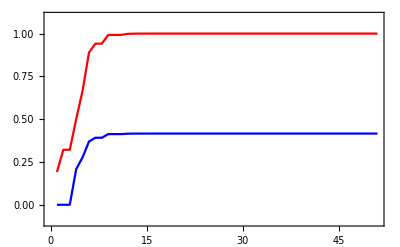

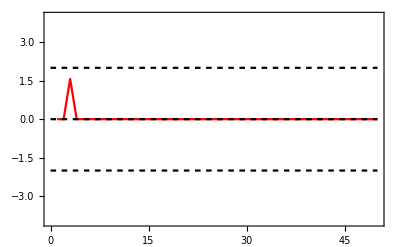

psi={0.455895+0.0115988 ⅈ,0.458845-0.285458 ⅈ,-4.25366×10^-9-6.83733×10^-9 ⅈ,1.72835×10^-10-6.79336×10^-9 ⅈ,1.72835×10^-10-6.79336×10^-9 ⅈ,-4.25366×10^-9-6.83733×10^-9 ⅈ,0.458845-0.285458 ⅈ,0.455895+0.0115988 ⅈ}

```mathematica
(*Z1Z2 terms*)
nmax=50;
maxiter=1000;
mbuffer=0;
fidval=Conjugate[psi].targetproj12.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};
mc=0;
md=0;

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
nc=RandomInteger[{0,ncdmax}];
nd=RandomInteger[{0,ncdmax}];
ptry=RandomReal[];
psi1=MCfunc12[nc,nd].psi;
prob1=Norm[psi1]^2;
(*Print[nc," ",nd," ",prob1," ",ptry];*)
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];
mc=mc+nc;
md=md+nd;

Eest=Eestfunc[mc,md];

If [(Abs[Eest-Etgt12]>=δtgt12)&&(mc+md>=mbuffer),
psi=Aflip12.psi;
mc=0;
md=0;

];

Eestlist=Append[Eestlist,Eest];

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj12.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
p1b=ListPlot[Eestlist,PlotStyle->{Red},PlotRange->{-4,4},Joined->True];
p3=Plot[DeleteDuplicates[En12],{x,0,nmax},PlotStyle->{Black,Dashing[0.01]}];
Show[p1]
Show[p1b,p3]
Print["psi=",Chop[psi]];
```

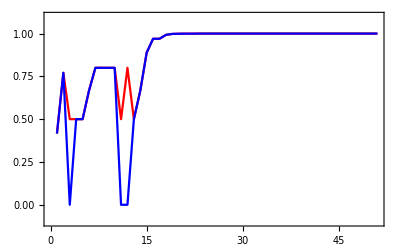

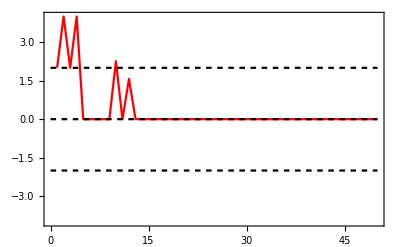

psi={-0.251801+0.660754 ⅈ,1.78232×10^-6+6.79207×10^-7 ⅈ,0,9.84601×10^-9+3.75212×10^-9 ⅈ,9.84601×10^-9+3.75212×10^-9 ⅈ,0,1.78232×10^-6+6.79207×10^-7 ⅈ,-0.251801+0.660754 ⅈ}

```mathematica
(*Z2Z3 terms*)
nmax=50;
maxiter=1000;
mbuffer=0;
fidval=Conjugate[psi].targetproj23.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};
mc=0;
md=0;

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
nc=RandomInteger[{0,ncdmax}];
nd=RandomInteger[{0,ncdmax}];
ptry=RandomReal[];
psi1=MCfunc23[nc,nd].psi;
prob1=Norm[psi1]^2;
(*Print[nc," ",nd," ",prob1," ",ptry];*)
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];
mc=mc+nc;
md=md+nd;

Eest=Eestfunc[mc,md];

If [(Abs[Eest-Etgt23]>=δtgt23)&&(mc+md>=mbuffer),
psi=Aflip34.psi;
mc=0;
md=0;

];

Eestlist=Append[Eestlist,Eest];

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj23.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
p1b=ListPlot[Eestlist,PlotStyle->{Red},PlotRange->{-4,4},Joined->True];
p3=Plot[DeleteDuplicates[En23],{x,0,nmax},PlotStyle->{Black,Dashing[0.01]}];
Show[p1]
Show[p1b,p3]
Print["psi=",Chop[psi]];
```

```mathematica
psic4
```

{1/2,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,1/2}

General::munfl: 0.0000641782^80 is too small to represent as a normalized machine number; precision may be lost.

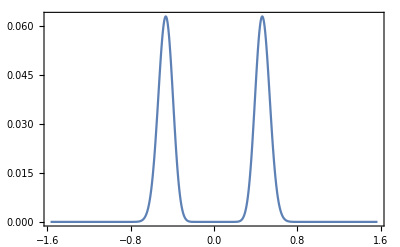

```mathematica
α=10.0;
nc=80;nd=20;
Plot[Cfunc[nc,nd,x],{x,-Pi/2,Pi/2},PlotRange->All]
```